```mathematica
$Assumptions = {Δ ∈ Reals, Δ < 0, x ∈ Reals, y ∈ Reals, a ∈ Reals, b ∈ Reals}
```

{Δ∈ℝ,Δ<0,x∈ℝ,y∈ℝ,a∈ℝ,b∈ℝ}

```mathematica
Unprotect[Conjugate];
Conjugate/:D[Conjugate[f_[x_]],x_]:=Conjugate[D[f[x],x]]
Protect[Conjugate];
Unprotect[Abs];
Abs/:D[Abs[f_[x_]],x_]:=Sign[f[x]]*D[f[x],x]
Protect[Abs];
```

# Prelims

```mathematica
G1 = (2π)/a{1, -1/Sqrt[3]}
G2 = (2π)/a{0, 2/Sqrt[3]}
G3 = -G1 - G2
Subscript[κ, 1]=2/3 G1 + 1/3 G2
Subscript[κ, 3]=Subscript[κ, 1]-G1
Subscript[κ, 5]=Subscript[κ, 1]+G3
Subscript[κ, 2]=1/3 G1 + 2/3 G2
Subscript[κ, 4]=Subscript[κ, 2]+G3
Subscript[κ, 6]=Subscript[κ, 2]-G2
```

{(2 π)/a,-(2 π)/(√3 a)}

{0,(4 π)/(√3 a)}

{-(2 π)/a,-(2 π)/(√3 a)}

{(4 π)/(3 a),0}

{-(2 π)/(3 a),(2 π)/(√3 a)}

{-(2 π)/(3 a),-(2 π)/(√3 a)}

{(2 π)/(3 a),(2 π)/(√3 a)}

{-(4 π)/(3 a),0}

{(2 π)/(3 a),-(2 π)/(√3 a)}

```mathematica
ω = Exp[I 2 π/3]
```

ⅇ^((2 ⅈ π)/3)

```mathematica
H0 = FullSimplify[{{0, Δ, Δ*}, {Δ*, 0, Δ}, {Δ, Δ*, 0}}]
```

{{0,Δ,Δ},{Δ,0,Δ},{Δ,Δ,0}}

```mathematica
δH = FullSimplify[ComplexExpand[{{0, α (ω q + ω* q*), α* (ω^2 q + ω^2* q*)}, {α* (ω q + ω* q*), 0, α (q + q*)}, {α (ω^2 q + ω^2* q*), α* (q + q*), 0}}, α]]
```

{{0,-q α,-q Conjugate[α]},{-q Conjugate[α],0,2 q α},{-q α,2 q Conjugate[α],0}}

```mathematica
ψ0 = FullSimplify[1/Sqrt[3]{1, ω^0, ω^(2*0)}]
ψ1 =FullSimplify[ 1/Sqrt[3]{1, ω^1, ω^(2*1)}]
ψ2 = FullSimplify[1/Sqrt[3]{1, ω^2, ω^(2*2)}]
```

{1/(√3),1/(√3),1/(√3)}

{1/(√3),(-1)^(2/3)/(√3),-(-1)^(1/3)/(√3)}

{1/(√3),-(-1)^(1/3)/(√3),(-1)^(2/3)/(√3)}

```mathematica
ϵ0 = FullSimplify[Δ* ω^0+Δ ω^(2*0)]
ϵ1 = FullSimplify[Δ* ω^1+Δ ω^(2*1)]
ϵ2 = FullSimplify[Δ* ω^2+Δ ω^(2*2)]
```

2 Δ

-Δ

-Δ

```mathematica
q = x + I y
```

x+ⅈ y

# PT 1st Order

```mathematica
ψ0p1 = FullSimplify[ComplexExpand[ψ0 + ((Conjugate[ψ1].(δH.ψ0))/(ϵ0 - ϵ1)ψ1 + (Conjugate[ψ2].(δH. ψ0))/(ϵ0 - ϵ2)ψ2 ), α]]
```

{(3 Δ-2 (x+ⅈ y) Re[α])/(3 √3 Δ),(3 (x α+ⅈ y α+Δ)-2 (x+ⅈ y) Re[α])/(3 √3 Δ),(3 Δ-(x+ⅈ y) (α-2 Conjugate[α]))/(3 √3 Δ)}

# PT 2nd Order

```mathematica
ψ0p2 = FullSimplify[ComplexExpand[ψ0p1+ ((Conjugate[ψ1].(δH .ψ2)*Conjugate[ψ2].(δH.ψ0))/((ϵ0 - ϵ1)*(ϵ0 - ϵ2))ψ1 + (Conjugate[ψ1].(δH.ψ1)*Conjugate[ψ1].(δH.ψ0))/((ϵ0 - ϵ1)*(ϵ0 - ϵ1))ψ1 + (Conjugate[ψ2].(δH.ψ1)*Conjugate[ψ1].(δH.ψ0))/((ϵ0 - ϵ2)*(ϵ0 - ϵ1))ψ2 + (Conjugate[ψ2].(δH.ψ2)*Conjugate[ψ2].(δH.ψ0))/((ϵ0 - ϵ2)*(ϵ0 - ϵ2))ψ2) - ((Conjugate[ψ1].(δH.ψ0)*Conjugate[ψ0].(δH.ψ0))/((ϵ0 - ϵ1)*(ϵ0 - ϵ1))ψ1 + (Conjugate[ψ2].(δH.ψ0)*Conjugate[ψ0].(δH.ψ0))/((ϵ0 - ϵ2)*(ϵ0 - ϵ2))ψ2) , α]]
```

{(9-(2 (x+ⅈ y) Re[α] (3 Δ+2 (x+ⅈ y) Re[α]))/Δ^2)/(9 √3),(9 Δ^2+(x+ⅈ y) (9 ⅈ Δ Im[α]+3 (Δ+2 (-ⅈ x+y) Im[α]) Re[α]+2 (x+ⅈ y) Re[α]^2))/(9 √3 Δ^2),(9 Δ^2+(x+ⅈ y) (-9 ⅈ Δ Im[α]+3 (Δ+2 ⅈ (x+ⅈ y) Im[α]) Re[α]+2 (x+ⅈ y) Re[α]^2))/(9 √3 Δ^2)}

```mathematica
ψ0p2 = FullSimplify[ComplexExpand[Normalize[ψ0p2], α]]
```

{(9 Δ^2-2 (x+ⅈ y) Re[α] (3 Δ+2 (x+ⅈ y) Re[α]))/(√(243 Δ^4+6 (x^2+y^2) (3 Im[α]^2 (9 Δ^2+4 Re[α] (-3 x Δ+(x^2+y^2) Re[α]))+Re[α]^2 (9 Δ^2+4 Re[α] (3 x Δ+(x^2+y^2) Re[α]))))),(9 Δ^2+(x+ⅈ y) (9 ⅈ Δ Im[α]+3 (Δ+2 (-ⅈ x+y) Im[α]) Re[α]+2 (x+ⅈ y) Re[α]^2))/(√(243 Δ^4+6 (x^2+y^2) (3 Im[α]^2 (9 Δ^2+4 Re[α] (-3 x Δ+(x^2+y^2) Re[α]))+Re[α]^2 (9 Δ^2+4 Re[α] (3 x Δ+(x^2+y^2) Re[α]))))),(9 Δ^2+(x+ⅈ y) (-9 ⅈ Δ Im[α]+3 (Δ+2 ⅈ (x+ⅈ y) Im[α]) Re[α]+2 (x+ⅈ y) Re[α]^2))/(√(243 Δ^4+6 (x^2+y^2) (3 Im[α]^2 (9 Δ^2+4 Re[α] (-3 x Δ+(x^2+y^2) Re[α]))+Re[α]^2 (9 Δ^2+4 Re[α] (3 x Δ+(x^2+y^2) Re[α])))))}

# Inner Radius

```mathematica
ux2 = FullSimplify[D[ψ0p2, x]]
```

{(-((9 Δ^2-2 (x+ⅈ y) Re[α] (3 Δ+2 (x+ⅈ y) Re[α])) (36 Im[α]^2 (-3 Δ+4 x Re[α]) (-3 x Δ+2 (x^2+y^2) Re[α])+12 Re[α]^2 (3 Δ+4 x Re[α]) (3 x Δ+2 (x^2+y^2) Re[α])))-4 Re[α] (3 Δ+4 (x+ⅈ y) Re[α]) (243 Δ^4+6 (x^2+y^2) (3 Im[α]^2 (9 Δ^2+4 Re[α] (-3 x Δ+(x^2+y^2) Re[α]))+Re[α]^2 (9 Δ^2+4 Re[α] (3 x Δ+(x^2+y^2) Re[α])))))/(2 (243 Δ^4+6 (x^2+y^2) (3 Im[α]^2 (9 Δ^2+4 Re[α] (-3 x Δ+(x^2+y^2) Re[α]))+Re[α]^2 (9 Δ^2+4 Re[α] (3 x Δ+(x^2+y^2) Re[α]))))^(3/2)),(-((36 Im[α]^2 (-3 Δ+4 x Re[α]) (-3 x Δ+2 (x^2+y^2) Re[α])+12 Re[α]^2 (3 Δ+4 x Re[α]) (3 x Δ+2 (x^2+y^2) Re[α])) (9 Δ^2+(x+ⅈ y) (9 ⅈ Δ Im[α]+3 (Δ+2 (-ⅈ x+y) Im[α]) Re[α]+2 (x+ⅈ y) Re[α]^2)))+2 (9 ⅈ Δ Im[α]+3 (Δ+4 (-ⅈ x+y) Im[α]) Re[α]+4 (x+ⅈ y) Re[α]^2) (243 Δ^4+6 (x^2+y^2) (3 Im[α]^2 (9 Δ^2+4 Re[α] (-3 x Δ+(x^2+y^2) Re[α]))+Re[α]^2 (9 Δ^2+4 Re[α] (3 x Δ+(x^2+y^2) Re[α])))))/(2 (243 Δ^4+6 (x^2+y^2) (3 Im[α]^2 (9 Δ^2+4 Re[α] (-3 x Δ+(x^2+y^2) Re[α]))+Re[α]^2 (9 Δ^2+4 Re[α] (3 x Δ+(x^2+y^2) Re[α]))))^(3/2)),(-2 (3 Im[α]^2 (-3 Δ+4 x Re[α]) (-3 x Δ+2 (x^2+y^2) Re[α])+Re[α]^2 (3 Δ+4 x Re[α]) (3 x Δ+2 (x^2+y^2) Re[α])) (9 Δ^2+(x+ⅈ y) (-9 ⅈ Δ Im[α]+3 (Δ+2 ⅈ (x+ⅈ y) Im[α]) Re[α]+2 (x+ⅈ y) Re[α]^2))+(-9 ⅈ Δ Im[α]+3 (Δ+4 ⅈ (x+ⅈ y) Im[α]) Re[α]+4 (x+ⅈ y) Re[α]^2) (81 Δ^4+2 (x^2+y^2) (3 Im[α]^2 (9 Δ^2+4 Re[α] (-3 x Δ+(x^2+y^2) Re[α]))+Re[α]^2 (9 Δ^2+4 Re[α] (3 x Δ+(x^2+y^2) Re[α])))))/(√3 (81 Δ^4+2 (x^2+y^2) (3 Im[α]^2 (9 Δ^2+4 Re[α] (-3 x Δ+(x^2+y^2) Re[α]))+Re[α]^2 (9 Δ^2+4 Re[α] (3 x Δ+(x^2+y^2) Re[α]))))^(3/2))}

```mathematica
uy2 = FullSimplify[D[ψ0p2, y]]
```

{(-12 y (9 Δ^2-2 (x+ⅈ y) Re[α] (3 Δ+2 (x+ⅈ y) Re[α])) (3 Im[α]^2 (9 Δ^2-12 x Δ Re[α]+8 (x^2+y^2) Re[α]^2)+Re[α]^2 (9 Δ^2+12 x Δ Re[α]+8 (x^2+y^2) Re[α]^2))-4 ⅈ Re[α] (3 Δ+4 (x+ⅈ y) Re[α]) (243 Δ^4+6 (x^2+y^2) (3 Im[α]^2 (9 Δ^2+4 Re[α] (-3 x Δ+(x^2+y^2) Re[α]))+Re[α]^2 (9 Δ^2+4 Re[α] (3 x Δ+(x^2+y^2) Re[α])))))/(2 (243 Δ^4+6 (x^2+y^2) (3 Im[α]^2 (9 Δ^2+4 Re[α] (-3 x Δ+(x^2+y^2) Re[α]))+Re[α]^2 (9 Δ^2+4 Re[α] (3 x Δ+(x^2+y^2) Re[α]))))^(3/2)),(-6 y (9 Δ^2+(x+ⅈ y) (9 ⅈ Δ Im[α]+3 (Δ+2 (-ⅈ x+y) Im[α]) Re[α]+2 (x+ⅈ y) Re[α]^2)) (3 Im[α]^2 (9 Δ^2-12 x Δ Re[α]+8 (x^2+y^2) Re[α]^2)+Re[α]^2 (9 Δ^2+12 x Δ Re[α]+8 (x^2+y^2) Re[α]^2))+(3 Im[α] (-3 Δ+4 (x+ⅈ y) Re[α])+ⅈ Re[α] (3 Δ+4 (x+ⅈ y) Re[α])) (243 Δ^4+6 (x^2+y^2) (3 Im[α]^2 (9 Δ^2+4 Re[α] (-3 x Δ+(x^2+y^2) Re[α]))+Re[α]^2 (9 Δ^2+4 Re[α] (3 x Δ+(x^2+y^2) Re[α])))))/(243 Δ^4+6 (x^2+y^2) (3 Im[α]^2 (9 Δ^2+4 Re[α] (-3 x Δ+(x^2+y^2) Re[α]))+Re[α]^2 (9 Δ^2+4 Re[α] (3 x Δ+(x^2+y^2) Re[α]))))^(3/2),(-6 y (9 Δ^2+(x+ⅈ y) (-9 ⅈ Δ Im[α]+3 (Δ+2 ⅈ (x+ⅈ y) Im[α]) Re[α]+2 (x+ⅈ y) Re[α]^2)) (3 Im[α]^2 (9 Δ^2-12 x Δ Re[α]+8 (x^2+y^2) Re[α]^2)+Re[α]^2 (9 Δ^2+12 x Δ Re[α]+8 (x^2+y^2) Re[α]^2))+(3 Im[α] (3 Δ-4 (x+ⅈ y) Re[α])+ⅈ Re[α] (3 Δ+4 (x+ⅈ y) Re[α])) (243 Δ^4+6 (x^2+y^2) (3 Im[α]^2 (9 Δ^2+4 Re[α] (-3 x Δ+(x^2+y^2) Re[α]))+Re[α]^2 (9 Δ^2+4 Re[α] (3 x Δ+(x^2+y^2) Re[α])))))/(243 Δ^4+6 (x^2+y^2) (3 Im[α]^2 (9 Δ^2+4 Re[α] (-3 x Δ+(x^2+y^2) Re[α]))+Re[α]^2 (9 Δ^2+4 Re[α] (3 x Δ+(x^2+y^2) Re[α]))))^(3/2)}

```mathematica
Ax = FullSimplify[ComplexExpand[Conjugate[ψ0p2].ux2, α]]
```

-((2 ⅈ y (3 Im[α]^2 (9 Δ^2-12 x Δ Re[α]+8 (x^2+y^2) Re[α]^2)+Re[α]^2 (9 Δ^2+12 x Δ Re[α]+8 (x^2+y^2) Re[α]^2)))/(81 Δ^4+2 (x^2+y^2) (3 Im[α]^2 (9 Δ^2+4 Re[α] (-3 x Δ+(x^2+y^2) Re[α]))+Re[α]^2 (9 Δ^2+4 Re[α] (3 x Δ+(x^2+y^2) Re[α])))))

```mathematica
Ay = FullSimplify[ComplexExpand[Conjugate[ψ0p2].uy2, α]]
```

(2 ⅈ (3 Im[α]^2 (-3 Δ+4 x Re[α]) (-3 x Δ+2 (x^2+y^2) Re[α])+Re[α]^2 (3 Δ+4 x Re[α]) (3 x Δ+2 (x^2+y^2) Re[α])))/(81 Δ^4+2 (x^2+y^2) (3 Im[α]^2 (9 Δ^2+4 Re[α] (-3 x Δ+(x^2+y^2) Re[α]))+Re[α]^2 (9 Δ^2+4 Re[α] (3 x Δ+(x^2+y^2) Re[α]))))

```mathematica
Ω = FullSimplify[I (D[Ay, x] - D[Ax, y])]
```

(108 Δ^2 (3 Δ^2 Re[α]^2 (-9 Δ^2-8 Re[α] (3 x Δ+2 (x^2+y^2) Re[α]))+Im[α]^2 (-81 Δ^4+8 Re[α] (27 x Δ^3-18 (x^2+y^2) Δ^2 Re[α]-4 (x^2+y^2)^2 Re[α]^3))))/(81 Δ^4+2 (x^2+y^2) (3 Im[α]^2 (9 Δ^2+4 Re[α] (-3 x Δ+(x^2+y^2) Re[α]))+Re[α]^2 (9 Δ^2+4 Re[α] (3 x Δ+(x^2+y^2) Re[α]))))^2

```mathematica
Ω = FullSimplify[-2 Im[ComplexExpand[Conjugate[ux2].uy2, α]]]
```

$Aborted

```mathematica
x = 0
y =0
```

0

0

```mathematica
FullSimplify[Ω]
```

-(4 (3 Im[α]^2+Re[α]^2))/(9 Δ^2)

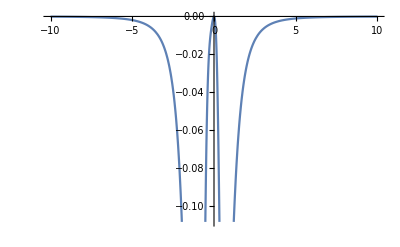

```mathematica
Plot[Ω, {α, -10, 10}]
```

```mathematica
χ1 =FullSimplify[Normalize[ {1, Norm[{x, y} + 
Subscript[κ, 1]] Exp[I * n * (ArcTan[(y + Last[Subscript[κ, 1]])/(x + First[Subscript[κ, 1]])])]}]]
```

{1/(√(1+ⅇ^(-2 Im[n ArcTan[(3 a y)/(4 π+3 a x)]]) (y^2+Abs[(4 π)/(3 a)+x]^2))),ⅇ^(ⅈ n ArcTan[(3 a y)/(4 π+3 a x)])/(√(ⅇ^(-2 Im[n ArcTan[(3 a y)/(4 π+3 a x)]])+1/(y^2+Abs[(4 π)/(3 a)+x]^2)))}

```mathematica
χ3=FullSimplify[Normalize[ {1, Norm[{x, y} + 
Subscript[κ, 3]] Exp[I * n * (ArcTan[(y + Last[Subscript[κ, 3]])/(x + First[Subscript[κ, 3]])])]}]]
```

{1/(√(1+ⅇ^(2 Im[n ArcTan[(2 √3 π+3 a y)/(2 π-3 a x)]]) (Abs[-(2 π)/(3 a)+x]^2+Abs[(2 π)/(√3 a)+y]^2))),ⅇ^(-ⅈ n ArcTan[(2 √3 π+3 a y)/(2 π-3 a x)])/(√(ⅇ^(2 Im[n ArcTan[(2 √3 π+3 a y)/(2 π-3 a x)]])+(9 a^2)/((2 π-3 a x)^2+(2 √3 π+3 a y)^2)))}

```mathematica
χ5=FullSimplify[Normalize[ {1, Norm[{x, y} + 
Subscript[κ, 5]] Exp[I * n * (ArcTan[(y + Last[Subscript[κ, 5]])/(x + First[Subscript[κ, 5]])])]}]]
```

{1/(√(1+ⅇ^(-2 Im[n ArcTan[(2 √3 π-3 a y)/(2 π-3 a x)]]) (Abs[-(2 π)/(3 a)+x]^2+Abs[-(2 π)/(√3 a)+y]^2))),ⅇ^(ⅈ n ArcTan[(2 √3 π-3 a y)/(2 π-3 a x)])/(√(ⅇ^(-2 Im[n ArcTan[(2 √3 π-3 a y)/(2 π-3 a x)]])+(9 a^2)/((2 π-3 a x)^2+(2 √3 π-3 a y)^2)))}

```mathematica
Clear[x, y, Δ, α]
```